Rearranging Lists

It’s common for lists that come out of one computation to have to be rearranged before going into another computation. For example, one might have a list of pairs, and need to convert it into a pair of lists, or vice versa.

Transpose a list of pairs so it becomes a pair of lists:

```mathematica
Transpose[{{1,2},{3,4},{5,6},{7,8},{9,10}}]
```

{{1,3,5,7,9},{2,4,6,8,10}}

Transpose the pair of lists back to a list of pairs:

```mathematica
Transpose[{{1,3,5,7,9},{2,4,6,8,10}}]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

Thread is a closely related operation, often useful for generating input to Graph.

“Thread” → across the elements of two lists:

```mathematica
Thread[{1,3,5,7,9}->{2,4,6,8,10}]
```

{1→2,3→4,5→6,7→8,9→10}

Partition takes a list, and partitions it into blocks of a specified size.

Partition a 12-element list into blocks of size 3:

```mathematica
Partition[Range[12],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

Partition a list of characters to display them in a grid:

```mathematica
Grid[Partition[Characters["An array of text made in the Wolfram Language"],9],Frame->All]
```

A | n |   | a | r | r | a | y |  
o | f |   | t | e | x | t |   | m
a | d | e |   | i | n |   | t | h
e |   | W | o | l | f | r | a | m
  | L | a | n | g | u | a | g | e

If you don’t tell it otherwise, Partition breaks a list up into non-overlapping blocks. But you can also tell it to break the list into blocks that have some specified offset.

Partition a list into blocks of size 3 with offset 1:

```mathematica
Partition[Range[10],3,1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10}}

Partition a list of characters into blocks with an offset of 1:

```mathematica
Grid[Partition[Characters["Wolfram Language"],12,1],Frame->All]
```

W | o | l | f | r | a | m |   | L | a | n | g
o | l | f | r | a | m |   | L | a | n | g | u
l | f | r | a | m |   | L | a | n | g | u | a
f | r | a | m |   | L | a | n | g | u | a | g
r | a | m |   | L | a | n | g | u | a | g | e

Use an offset of 2 instead:

```mathematica
Grid[Partition[Characters["Wolfram Language"],12,2],Frame->All]
```

W | o | l | f | r | a | m |   | L | a | n | g
l | f | r | a | m |   | L | a | n | g | u | a
r | a | m |   | L | a | n | g | u | a | g | e

Partition takes a list and breaks it into sublists. Flatten “flattens out” sublists.

Make a list of lists from digits of successive integers:

```mathematica
IntegerDigits/@Range[20]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0}}

Make a flattened version:

```mathematica
Flatten[IntegerDigits/@Range[20]]
```

{1,2,3,4,5,6,7,8,9,1,0,1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,2,0}

Make a plot from the sequence of digits:

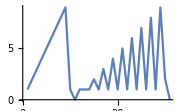

```mathematica
ListLinePlot[Flatten[IntegerDigits/@Range[20]]]
```

Flatten will normally flatten out all levels of lists. But quite often you only want to flatten, say, one level of lists. This makes a 4×4 table in which each element is itself a list.

Make a list of lists of lists:

```mathematica
Table[IntegerDigits[i^j],{i,4},{j,4}]
```

{{{1},{1},{1},{1}},{{2},{4},{8},{1,6}},{{3},{9},{2,7},{8,1}},{{4},{1,6},{6,4},{2,5,6}}}

Flatten everything out:

```mathematica
Flatten[Table[IntegerDigits[i^j],{i,4},{j,4}]]
```

{1,1,1,1,2,4,8,1,6,3,9,2,7,8,1,4,1,6,6,4,2,5,6}

Flatten out only one level of list:

```mathematica
Flatten[Table[IntegerDigits[i^j],{i,4},{j,4}],1]
```

{{1},{1},{1},{1},{2},{4},{8},{1,6},{3},{9},{2,7},{8,1},{4},{1,6},{6,4},{2,5,6}}

ArrayFlatten is a generalization of Flatten, which takes arrays of arrays, and flattens them into individual arrays.

This generates a deeply nested structure that’s hard to understand:

```mathematica
NestList[{{#,0},{#,#}}&,{{1}},2]
```

{{{1}},{{{{1}},0},{{{1}},{{1}}}},{{{{{{1}},0},{{{1}},{{1}}}},0},{{{{{1}},0},{{{1}},{{1}}}},{{{{1}},0},{{{1}},{{1}}}}}}}

ArrayFlatten makes a structure that’s a little easier to understand:

```mathematica
NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},2]
```

{{{1}},{{1,0},{1,1}},{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,1,1,1}}}

With ArrayPlot, it’s considerably easier to see what’s going on:

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Generate a fractal Sierpinski pattern with 8 levels of nesting:

```mathematica
ArrayPlot[Nest[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},8]]
```

-Graphics-

There are many other ways to rearrange lists. For example, Split splits a list into runs of identical elements.

Split a list into sequences of successive identical elements:

```mathematica
Split[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1},{2,2},{1,1},{3},{1,1,1},{2}}

Gather, on the other hand, gathers identical elements together, wherever they appear.

Gather identical elements together in lists:

```mathematica
Gather[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1,1,1,1,1,1},{2,2,2},{3}}

GatherBy gathers elements according to the result of applying a function to them. Here it’s using LetterQ, so that it gathers separately letters and non-letters.

Gather characters according to whether they are letters or not:

```mathematica
GatherBy[Characters["It's true that 2+2 is equal to 4!"],LetterQ]
```

{{I,t,s,t,r,u,e,t,h,a,t,i,s,e,q,u,a,l,t,o},{', , , ,2,+,2, , , , ,4,!}}

SortBy sorts according to the result of applying a function.

Sort normally sorts shorter lists before longer ones:

```mathematica
Sort[Table[IntegerDigits[2^n],{n,10}]]
```

{{2},{4},{8},{1,6},{3,2},{6,4},{1,2,8},{2,5,6},{5,1,2},{1,0,2,4}}

Here SortBy is told to sort by the first element in each list:

```mathematica
SortBy[Table[IntegerDigits[2^n],{n,10}],First]
```

{{1,6},{1,2,8},{1,0,2,4},{2},{2,5,6},{3,2},{4},{5,1,2},{6,4},{8}}

Sort sorts a list in order. Union also removes any repeated elements.

Find all the distinct elements that appear:

```mathematica
Union[{1,9,5,3,1,4,3,1,3,3,5,3,9}]
```

{1,3,4,5,9}

You can use Union to find the “union” of elements that appear in any of several lists.

Get a list of all elements that appear in any of the lists:

```mathematica
Union[{2,1,3,7,9},{4,5,1,2,3,3},{3,1,2,8,5}]
```

{1,2,3,4,5,7,8,9}

Find which elements are common to all the lists:

```mathematica
Intersection[{2,1,3,7,9},{4,5,1,2,3,3},{3,1,2,8}]
```

{1,2,3}

Find which elements are in the first list but not the second one:

```mathematica
Complement[{4,5,1,2,3,3},{3,1,2,8}]
```

{4,5}

Find letters that appear in any of English, Swedish and Turkish:

```mathematica
Union[Alphabet["English"],Alphabet["Swedish"],Alphabet["Turkish"]]
```

{ğ,ş,a,å,ä,b,c,ç,d,e,f,g,h,i,ı,j,k,l,m,n,o,ö,p,q,r,s,t,u,ü,v,w,x,y,z}

Letters that appear in Swedish but not English:

```mathematica
Complement[Alphabet["Swedish"],Alphabet["English"]]
```

{å,ä,ö}

Another of the many functions you can apply to lists is Riffle, which inserts things between successive elements of a list.

Riffle x in between the elements of a list:

```mathematica
Riffle[{1,2,3,4,5},x]
```

{1,x,2,x,3,x,4,x,5}

Riffle -- into a list of characters:

```mathematica
Riffle[Characters["WOLFRAM"],"--"]
```

{W,--,O,--,L,--,F,--,R,--,A,--,M}

Join everything together in a single string:

```mathematica
StringJoin[Riffle[Characters["WOLFRAM"],"--"]]
```

W--O--L--F--R--A--M

Functions like Partition let you take a list and break it into sublists. Sometimes you’ll instead just want to start from a collection of possible elements, and form lists from them.

Permutations gives all possible orderings, or permutations, of a list.

Generate a list of the 3!=3×2×1=6 possible orderings of 3 elements:

```mathematica
Permutations[{Red,Green,Blue}]
```

{{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}}

Generate all 2^3=8 possible subsets of a list of 3 elements:

```mathematica
Subsets[{Red,Green,Blue}]
```

{{},{RGBColor[1, 0, 0]},{RGBColor[0, 1, 0]},{RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}

Tuples takes a list of elements, and generates all possible combinations of a given number of those elements.

Generate a list of all possible triples of red and green:

```mathematica
Tuples[{Red,Green},3]
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}}

RandomChoice lets you make a random choice from a list of elements.

Make a single random choice from a list:

```mathematica
RandomChoice[{Red,Green,Blue}]
```

RGBColor[0, 1, 0]

Make a list of 20 random choices:

```mathematica
RandomChoice[{Red,Green,Blue},20]
```

{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

Make 5 lists of 3 random choices:

```mathematica
RandomChoice[{Red,Green,Blue},{5,3}]
```

{{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}}

RandomSample picks a random sample of elements from a list, never picking any particular element more than once.

Pick 20 elements from the range 1 to 100, never picking any number more than once:

```mathematica
RandomSample[Range[100],20]
```

{82,3,93,92,39,45,63,32,79,75,34,1,11,59,98,67,38,44,28,76}

If you don’t say how many elements to pick you get a random ordering of the whole list:

```mathematica
RandomSample[Range[10]]
```

{2,5,1,7,4,6,3,8,9,10}

Vocabulary

Transpose[list] |   | transpose inner and outer lists 
Thread[list_1→list_2] |   | thread across elements of lists 
Partition[list,n] |   | partition into blocks of size n 
Flatten[list] |   | flatten out all sublists 
Flatten[list,k] |   | flatten out k levels of sublists 
ArrayFlatten[list] |   | flatten arrays of arrays 
Split[list] |   | split into runs of identical elements 
Gather[list] |   | gather identical elements into lists 
GatherBy[list,f] |   | gather according to results of applying  f 
SortBy[list,f] |   | sort according to results of applying  f  
Riffle[list,x] |   | riffle x between elements of list 
Union[list] |   | distinct elements in list
Union[list_1,list_2, ...] |   | elements that appear in any of the lists
Intersection[list_1,list_2, ...] |   | elements that appear in all the lists
Complement[list_1,list_2] |   | elements that appear in list_1 but not list_2
Permutations[list] |   | all possible permutations (orderings) 
Subsets[list] |   | all possible subsets 
Tuples[list,n] |   | all possible combinations of n elements 
RandomChoice[list] |   | random choice from list 
RandomChoice[list,n] |   | n random choices 
RandomSample[list,n] |   | n random non-repeating samples 
RandomSample[list] |   | random ordering of a list

"21 Exercises Available"
"with 13 extras" | "Get Started »"

Use Thread to make a list of rules with each letter of the alphabet going to its position in the alphabet. »

| Expected output: |  
  | {"a"→1,"b"→2,"c"→3,"d"→4,"e"→5,"f"→6,"g"→7,"h"→8,"i"→9,"j"→10,"k"→11,"l"→12,"m"→13,"n"→14,"o"→15,"p"→16,"q"→17,"r"→18,"s"→19,"t"→20,"u"→21,"v"→22,"w"→23,"x"→24,"y"→25,"z"→26} |

Make a 4×6 grid of the first 24 letters of the alphabet. »

| Expected output: |  
  | "a" | "b" | "c" | "d" | "e" | "f"
"g" | "h" | "i" | "j" | "k" | "l"
"m" | "n" | "o" | "p" | "q" | "r"
"s" | "t" | "u" | "v" | "w" | "x" |

Make a grid of the digits in 2^1000, with 50 digits per row, and put frames around everything. »

| Expected output: |  
  | 1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3 |

Make a grid of the first 400 characters in the Wikipedia article for “computers”, with 20 characters per row, and frames around everything. »

| Sample expected output: |  
  | "A" | " " | "c" | "o" | "m" | "p" | "u" | "t" | "e" | "r" | " " | "i" | "s" | " " | "a" | " " | "g" | "e" | "n" | "e"
"r" | "a" | "l" | "-" | "p" | "u" | "r" | "p" | "o" | "s" | "e" | " " | "d" | "e" | "v" | "i" | "c" | "e" | " " | "t"
"h" | "a" | "t" | " " | "c" | "a" | "n" | " " | "b" | "e" | " " | "p" | "r" | "o" | "g" | "r" | "a" | "m" | "m" | "e"
"d" | " " | "t" | "o" | " " | "c" | "a" | "r" | "r" | "y" | " " | "o" | "u" | "t" | " " | "a" | " " | "s" | "e" | "t"
" " | "o" | "f" | " " | "a" | "r" | "i" | "t" | "h" | "m" | "e" | "t" | "i" | "c" | " " | "o" | "r" | " " | "l" | "o"
"g" | "i" | "c" | "a" | "l" | " " | "o" | "p" | "e" | "r" | "a" | "t" | "i" | "o" | "n" | "s" | " " | "a" | "u" | "t"
"o" | "m" | "a" | "t" | "i" | "c" | "a" | "l" | "l" | "y" | "." | " " | "S" | "i" | "n" | "c" | "e" | " " | "a" | " "
"s" | "e" | "q" | "u" | "e" | "n" | "c" | "e" | " " | "o" | "f" | " " | "o" | "p" | "e" | "r" | "a" | "t" | "i" | "o"
"n" | "s" | " " | "c" | "a" | "n" | " " | "b" | "e" | " " | "r" | "e" | "a" | "d" | "i" | "l" | "y" | " " | "c" | "h"
"a" | "n" | "g" | "e" | "d" | "," | " " | "t" | "h" | "e" | " " | "c" | "o" | "m" | "p" | "u" | "t" | "e" | "r" | " "
"c" | "a" | "n" | " " | "s" | "o" | "l" | "v" | "e" | " " | "m" | "o" | "r" | "e" | " " | "t" | "h" | "a" | "n" | " "
"o" | "n" | "e" | " " | "k" | "i" | "n" | "d" | " " | "o" | "f" | " " | "p" | "r" | "o" | "b" | "l" | "e" | "m" | "."
"
" | "C" | "o" | "n" | "v" | "e" | "n" | "t" | "i" | "o" | "n" | "a" | "l" | "l" | "y" | "," | " " | "a" | " " | "c"
"o" | "m" | "p" | "u" | "t" | "e" | "r" | " " | "c" | "o" | "n" | "s" | "i" | "s" | "t" | "s" | " " | "o" | "f" | " "
"a" | "t" | " " | "l" | "e" | "a" | "s" | "t" | " " | "o" | "n" | "e" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s"
"i" | "n" | "g" | " " | "e" | "l" | "e" | "m" | "e" | "n" | "t" | "," | " " | "t" | "y" | "p" | "i" | "c" | "a" | "l"
"l" | "y" | " " | "a" | " " | "c" | "e" | "n" | "t" | "r" | "a" | "l" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s"
"i" | "n" | "g" | " " | "u" | "n" | "i" | "t" | " " | "(" | "C" | "P" | "U" | ")" | "," | " " | "a" | "n" | "d" | " "
"s" | "o" | "m" | "e" | " " | "f" | "o" | "r" | "m" | " " | "o" | "f" | " " | "m" | "e" | "m" | "o" | "r" | "y" | "."
" " | "T" | "h" | "e" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s" | "i" | "n" | "g" | " " | "e" | "l" | "e" | "m" |

Make a line plot of the flattened list of the digits from the numbers from 0 to 200 (Champernowne sequence). »

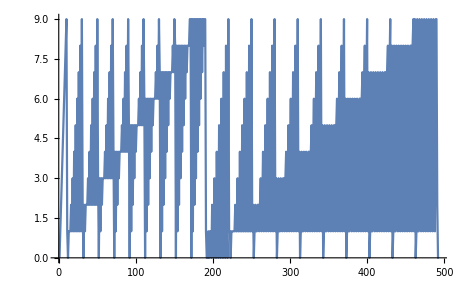
| Expected output: |  
  | -Graphics- |

Make 4 steps in the “Menger sponge” analog of the fractal Sierpinski pattern from the text, but with a “kernel” of the form {{#,#,#},{#,0,#},{#,#,#}}. »


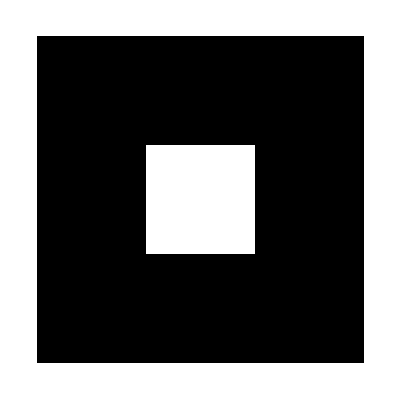
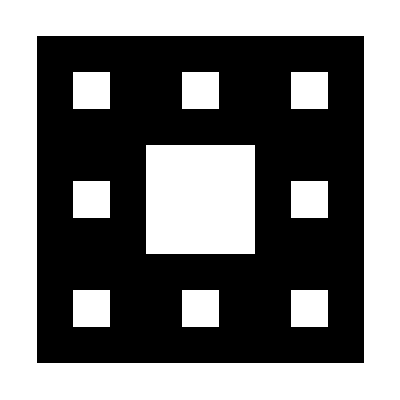
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Find Pythagorean triples involving only integers by selecting {x,y,Sqrt[x^2+y^2]} with x and y up to 20. »

| Expected output: |  
  | {{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}} |

Find the lengths of the longest sequences of identical digits in 2^n for n up to 100. »

| Expected output: |  
  | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2} |

Take the names of integers up to 100 and gather them into sublists according to their first letters. »

| Expected output: |  
  | {{"one","one hundred"},{"two","three","ten","twelve","thirteen","twenty","twenty-one","twenty-two","twenty-three","twenty-four","twenty-five","twenty-six","twenty-seven","twenty-eight","twenty-nine","thirty","thirty-one","thirty-two","thirty-three","thirty-four","thirty-five","thirty-six","thirty-seven","thirty-eight","thirty-nine"},{"four","five","fourteen","fifteen","forty","forty-one","forty-two","forty-three","forty-four","forty-five","forty-six","forty-seven","forty-eight","forty-nine","fifty","fifty-one","fifty-two","fifty-three","fifty-four","fifty-five","fifty-six","fifty-seven","fifty-eight","fifty-nine"},{"six","seven","sixteen","seventeen","sixty","sixty-one","sixty-two","sixty-three","sixty-four","sixty-five","sixty-six","sixty-seven","sixty-eight","sixty-nine","seventy","seventy-one","seventy-two","seventy-three","seventy-four","seventy-five","seventy-six","seventy-seven","seventy-eight","seventy-nine"},{"eight","eleven","eighteen","eighty","eighty-one","eighty-two","eighty-three","eighty-four","eighty-five","eighty-six","eighty-seven","eighty-eight","eighty-nine"},{"nine","nineteen","ninety","ninety-one","ninety-two","ninety-three","ninety-four","ninety-five","ninety-six","ninety-seven","ninety-eight","ninety-nine"}} |

Sort the first 50 words in WordList[ ] by their last letters. »

| Expected output: |  
  | {"a","abandoned","abashed","abbreviated","abed","abalone","abase","abate","abbe","abbreviate","abdicate","abeyance","abhorrence","abidance","abide","abducting","abiding","aah","abash","aardvark","aback","abdominal","abeam","abandon","abbreviation","abdication","abdomen","abduction","aberration","abjection","abattoir","abductor","abettor","abhor","abacus","abbess","abaft","abandonment","abasement","abashment","abatement","abbot","abduct","aberrant","abet","abhorrent","abject","abbey","ability","abjectly"} |

Make a list of the first 20 squares, sorted by their first digits. »

| Expected output: |  
  | {1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9} |

Sort integers up to 20 by the length of their names in English. »

| Expected output: |  
  | {1,2,6,10,4,5,9,3,7,8,11,12,20,15,16,13,14,18,19,17} |

Get a random sample of 20 words from WordList[ ], and gather them into sublists by length. »

| Sample expected output: |  
  | {{"paste"},{"mistakenly","unintended","victorious","watercress"},{"powerful","jingoist","ballpark","rapeseed","dyslexia"},{"repeal"},{"paleontological"},{"encouragement"},{"countryside"},{"selfish","hedging"},{"barometer"},{"veil","well"},{"municipality"}} |

Find letters that appear in Ukrainian but not Russian. »

| Expected output: |  
  | {"є","і","ї","ґ"} |

Use Intersection to find numbers that appear both among the first 100 squares and cubes. »

| Expected output: |  
  | {1,64,729,4096} |

Find the list of countries that are in both NATO and the G8. »

| Expected output: |  
  | {"Canada","France","Germany","Italy","United Kingdom","United States"} |

Make a grid in which all possible permutations of the numbers 1 through 4 appear as successive columns. »

| Expected output: |  
  | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1 |

Make a list of all the different strings that can be obtained by permuting the characters in “hello”. »

| Expected output: |  
  | {"ehllo","ehlol","eholl","elhlo","elhol","ellho","elloh","elohl","elolh","eohll","eolhl","eollh","hello","helol","heoll","hlelo","hleol","hlleo","hlloe","hloel","hlole","hoell","holel","holle","lehlo","lehol","lelho","leloh","leohl","leolh","lhelo","lheol","lhleo","lhloe","lhoel","lhole","lleho","lleoh","llheo","llhoe","lloeh","llohe","loehl","loelh","lohel","lohle","loleh","lolhe","oehll","oelhl","oellh","ohell","ohlel","ohlle","olehl","olelh","olhel","olhle","olleh","ollhe"} |

Make an array plot of the sequence of possible 5-tuples of 0 and 1. »

| Expected output: |  
  |  |

Generate a list of 10 random sequences of 5 letters. »

| Sample expected output: |  
  | {"ayasl","icnry","ahbaa","jqkpc","orlaf","rmexo","ngrfy","vwhii","wjiqn","gngvk"} |

Find a simpler form for Flatten[Table[{i,j,k},{i,2},{j,2},{k,2}],2]. »

| Expected output: |  
  | {{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}} |

Make an array plot from the numbers of the letters in the first 1000 characters in the Wikipedia article on “computers”, with 30 letters per row. »

| Expected output: |  
  | -Graphics- |

Gather integers up to 30 into lists based on their values modulo 3. »

| Expected output: |  
  | {{1,4,7,10,13,16,19,22,25,28},{2,5,8,11,14,17,20,23,26,29},{3,6,9,12,15,18,21,24,27,30}} |

Gather the first 50 powers of 2 according to their last digits. »

| Expected output: |  
  | {{2,32,512,8192,131072,2097152,33554432,536870912,8589934592,137438953472,2199023255552,35184372088832,562949953421312},{4,64,1024,16384,262144,4194304,67108864,1073741824,17179869184,274877906944,4398046511104,70368744177664,1125899906842624},{8,128,2048,32768,524288,8388608,134217728,2147483648,34359738368,549755813888,8796093022208,140737488355328},{16,256,4096,65536,1048576,16777216,268435456,4294967296,68719476736,1099511627776,17592186044416,281474976710656}} |

Make a line plot of the result of sorting the numbers from −10 to +10 by their absolute values. »

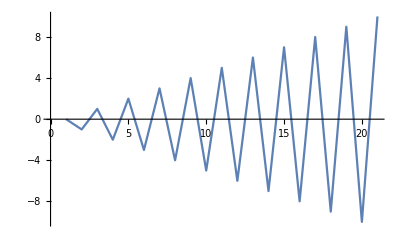
| Expected output: |  
  | -Graphics- |

Make a line plot of the list of the first 200 squares, sorted by their first digits. »

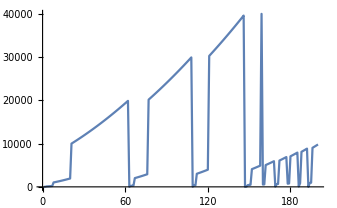
| Expected output: |  
  | -Graphics- |

Make a line plot of integers up to 200 sorted by the lengths of their names in English. »

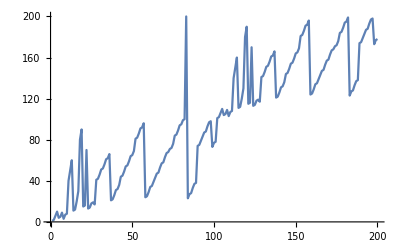
| Expected output: |  
  | -Graphics- |

Get a random sample of 25 words from WordList[]. »

| Expected output: |  
  | {"autopsy","reclassification","advancement","forswear","swimwear","cravat","cyclone","taps","diplomatic","effacement","peaked","ponderously","publication","immune","outstay","petrol","deaf","bilk","oddments","scoreboard","lifeless","debriefing","radiogram","doting","inter"} |

Riffle periods into the string “UNCLE” to make “U.N.C.L.E.”. »

| Expected output: |  
  | "U.N.C.L.E." |

Find letters that appear in Swedish or Polish but not English. »

| Expected output: |  
  | {"ą","ę","ń","ś","ź","ż","å","ä","ć","ł","ó","ö"} |

Find countries that are in the World Health Organization but not the United Nations. »

| Expected output: |  
  | {"Cook Islands","Niue"} |

Make a list of all pair-wise blends of red, green and blue. »

| Expected output: |  
  | {RGBColor[1, 0, 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, 0, 1]} |

Make a list of array plots, each 50 rows high and with image size 50, of successive possible 8-tuples of 0 and 1. »

| Expected output: |  
  | {,,,,} |

Generate 1000 random sequences of 4 letters, and make a list of ones that appear in WordList[ ].  »

| Expected output: |  
  | {"avow","frog","know","lido","snot"} |

Q&A

What does Partition do if the blocks don’t fit perfectly?

If it’s not told otherwise, it’ll only include complete blocks, so it’ll just drop elements that appear only in incomplete blocks. However, if you say for example Partition[list,UpTo[4]], it’ll make blocks up to length 4, with the last block being shorter if necessary.

Tech Note

Transpose can be thought of as transposing rows and columns in a matrix.

ArrayFlatten flattens an array of arrays into a single array, or alternatively, a matrix of matrices into a single matrix.

DeleteDuplicates[list] does the same as Union[list], except it doesn’t reorder elements.

More to Explore

Guide to Rearranging & Restructuring Lists in the Wolfram Language »